```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]]
```

/Users/tazz/Documents/Git/StabilityProject2014

```mathematica
"/Users/ethanspangler/StabilityProject"
```

/Users/ethanspangler/StabilityProject

Plots of Freedonia, Merika, and Kleptopia for low initial dissent.

```mathematica
Freedonia =Import["dataFreedonia.mx"] // Dataset;
Merika =Import["dataMerika.mx"] // Dataset;
Kleptopia=Import["dataKleptopia.mx"]//Dataset;
Cathay=Import["dataCathay.mx"]//Dataset;
Rentistan=Import["dataRentistan.mx"]//Dataset;
Develpolus=Import["dataDevelpolus.mx"]//Dataset;
Bellicostia=Import["dataBellicostia.mx"]//Dataset;
Hippieberg=Import["dataHippieberg.mx"]//Dataset;
```

New lines to convert Scientific form to plotable form:

```mathematica
Freedonia = Freedonia/.ScientificForm[n_,rest___]->n
Merika = Merika/.ScientificForm[n_,rest___]->n
Kleptopia = Kleptopia/.ScientificForm[n_,rest___]->n
Cathay= Cathay/.ScientificForm[n_,rest___]->n
Rentistan= Rentistan/.ScientificForm[n_,rest___]->n
Develpolus= Develpolus/.ScientificForm[n_,rest___]->n
Bellicostia= Bellicostia/.ScientificForm[n_,rest___]->n
Hippieberg= Hippieberg/.ScientificForm[n_,rest___]->n
```

0. | 0.03959 | 6.3×10^7 | 2.87×10^8 | 1.605×10^1355718576299609
1. | 0.03557 | 3.611×10^7 | 3.139×10^8 | 0.004011
2 levels | 2rows |  |  |  | Dataset[{__List}]

0. | 0.04573 | 9.1×10^7 | 2.59×10^8 | 1.605×10^1355718576299609
1. | 0.04188 | 7.096×10^7 | 2.79×10^8 | 0.003854
2 levels | 2rows |  |  |  | Dataset[{__List}]

0. | 1.069 | 4.1×10^7 | 9.×10^6 | 1.605×10^1355718576299609
1. | 1.072 | 4.072×10^7 | 9.276×10^6 | 0.002852
2 levels | 2rows |  |  |  | Dataset[{__List}]

0 | 10000 Mean[{}] | 9.15×10^7 | 5.85×10^7 | Abs[1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609-10000 Mean[{}]]
2 levels | 1rows |  |  |  | Dataset[{__List}]

0 | 10000 Mean[{}] | 1.5×10^8 | 1.5×10^8 | Abs[1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609-10000 Mean[{}]]
2 levels | 1rows |  |  |  | Dataset[{__List}]

0 | 10000 Mean[{}] | 5.×10^7 | 5.×10^7 | Abs[1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609-10000 Mean[{}]]
2 levels | 1rows |  |  |  | Dataset[{__List}]

0 | 10000 Mean[{}] | 4.6×10^7 | 4.×10^6 | Abs[1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609-10000 Mean[{}]]
2 levels | 1rows |  |  |  | Dataset[{__List}]

0 | 10000 Mean[{}] | 4.×10^6 | 4.6×10^7 | Abs[1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609-10000 Mean[{}]]
2 levels | 1rows |  |  |  | Dataset[{__List}]

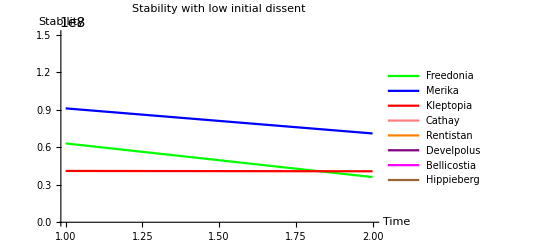

```mathematica
ListLinePlot[{Freedonia[All,3]//Normal,Merika[All,3]//Normal,Kleptopia[All,3] //Normal ,
Cathay[All,3]//Normal,
Rentistan[All,3]//Normal,
Develpolus[All,3] //Normal,
Bellicostia[All,3]//Normal,
Hippieberg[All,3]//Normal},PlotLegends->{"Freedonia","Merika","Kleptopia","Cathay","Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{Green,Blue,Red,Pink,Orange,Purple,Magenta,Brown},
PlotLabel->Style["Stability with low initial dissent", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}]
```

```mathematica
3
```